# This is a guide to using the NDSolve function in Mathematica

This function can be tricky to use and understand the outputs that Mathematica is providing.

First, Using the NDSolve function returns what is known as a rule in Mathematica.

```mathematica
s=NDSolve[{f''[t]+Sin[f[t]]==0,f[0]==Pi/8,f'[0]==0},f,{t,0,10}]
```

{{f→InterpolatingFunction[…]}}

To convert a rule to a function, you do this bit of magic that I do not understand:

```mathematica
ph=f/.First[s]
```

InterpolatingFunction[…]

Now I have a function that I can evaluate and understand in the normal way.

```mathematica
ph[0]
```

0.392699

I can plot this function just like any other.

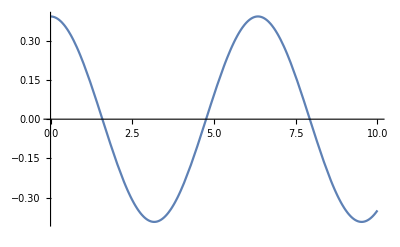

```mathematica
Plot[ph[t],{t,0,10}]
```

And parametric plots are particularly helpful for this example type of differential equations (pendulum).

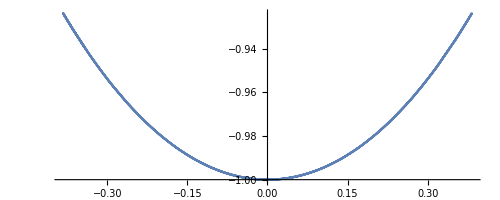

```mathematica
ParametricPlot[{Sin[ph[t]],-Cos[ph[t]]},{t,0,10}]
```